```mathematica
Clear[G11,G22,G12,Nulls,P,G]
```

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0,Jtwo,-0.1,z]-G22[1,0,Jtwo,-0.1,z]-G12[1,0,Jtwo,-0.1,z]^2+G11[1,0,Jtwo,-0.1,z]G22[1,0,Jtwo,-0.1,z]
FindRoot[Nulls[-0.005,z]==0,{z,0.9}]
```

{z→0.899865}

```mathematica
√(J^4/(J^2+J u)+(J^3 u)/(J^2+J u)+(J^2 u^2)/(2 (J^2+J u))+(J u^3)/(8 (J^2+J u))-1/(8 (J^2+J u))(√(256 J^4 J q^2+512 J^3 J q^2 u+64 J^6 u^2+320 J^2 J q^2 u^2+96 J^5 u^3+64 J  J q^2 u^3+52 J^4 u^4+12 J^3 u^5+J^2 u^6)))/.{J->1,q->0,u->2*-0.1}
```

0.9

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.9]]
```

{{0.005,0.899866},{0.01,0.899464},{0.015,0.898797},{0.02,0.897869},{0.025,0.896687},{0.03,0.895256},{0.035,0.893584},{0.04,0.89168},{0.045,0.889553},{0.05,0.887211},{0.055,0.884664},{0.06,0.881922},{0.065,0.878994},{0.07,0.875889},{0.075,0.872616},{0.08,0.869183},{0.085,0.865597},{0.09,0.861868},{0.095,0.858},{0.1,0.854001}}

```mathematica
moduler[Lister[-1,-0.005,0.9]]
```

{{-0.005,0.899865},{-0.01,0.899462},{-0.015,0.898793},{-0.02,0.89786},{-0.025,0.896668},{-0.03,0.895225},{-0.035,0.893535},{-0.04,0.891609},{-0.045,0.889453},{-0.05,0.887078},{-0.055,0.884492},{-0.06,0.881705},{-0.065,0.878726},{-0.07,0.875564},{-0.075,0.872229},{-0.08,0.868728},{-0.085,0.86507},{-0.09,0.861262},{-0.095,0.857312},{-0.1,0.853226}}

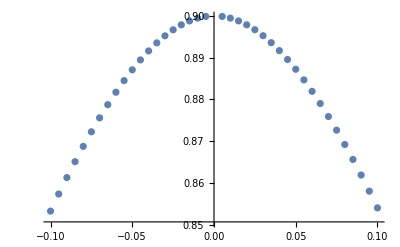

```mathematica
P = ListPlot[{{0.005,0.8998656399912153},{0.01,0.8994636537963471},{0.015,0.8987968265064384},{0.02,0.8978693888132562},{0.025,0.8966868811759011},{0.03,0.8952559838794547},{0.035,0.8935843243111518},{0.04,0.8916802731308007},{0.045,0.8895527402177427},{0.05,0.8872109796327129},{0.055,0.8846644106868747},{0.06,0.8819224599016988},{0.065,0.8789944264623966},{0.07,0.8758893718873828},{0.075,0.8726160331727614},{0.08,0.8691827576385857},{0.085,0.8655974570557619},{0.09,0.861867578331839},{0.095,0.8580000879745328},{0.1,0.8540014676763447},{-0.005,0.8998654863428212},{-0.01,0.8994624304483313},{-0.015,0.8987927300707611},{-0.02,0.8978597838164608},{-0.025,0.8966683777860729},{-0.03,0.8952245326893282},{-0.035,0.8935353220544772},{-0.04,0.8916086731702563},{-0.045,0.88945316217508},{-0.05,0.8870778134738458},{-0.055,0.884491911738461},{-0.06,0.8817048324895824},{-0.065,0.8787258949815372},{-0.07,0.87556423906084},{-0.075,0.8722287259794512},{-0.08,0.86872786189172},{-0.085,0.8650697419139568},{-0.09,0.8612620121599831},{-0.095,0.8573118469824297},{-0.1,0.8532259386882597}}]
```

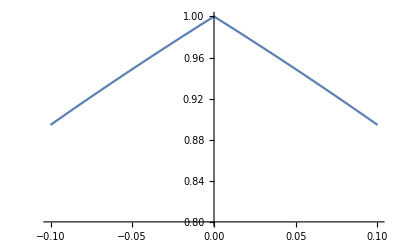

```mathematica
G = Plot[Sqrt[1+2*J*Cos[2*Inv[0,J]]],{J,-0.1,0.1},PlotRange->{0.8,1}]
```

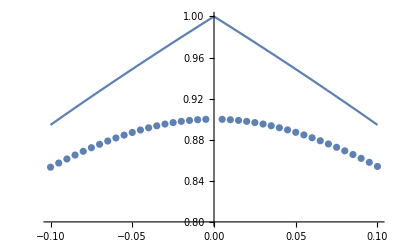

```mathematica
Show[G,P]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
differ[-1,0,moduler[Lister[-1,-0.005,0.9]]]
```

{{-0.005,0.095122},{-0.01,0.0904871},{-0.015,0.0860931},{-0.02,0.0819361},{-0.025,0.0780111},{-0.03,0.0743114},{-0.035,0.0708298},{-0.04,0.0675576},{-0.045,0.064486},{-0.05,0.0616055},{-0.055,0.0589062},{-0.06,0.0563783},{-0.065,0.054012},{-0.07,0.0517976},{-0.075,0.0497257},{-0.08,0.0477873},{-0.085,0.0459736},{-0.09,0.0442765},{-0.095,0.0426882},{-0.1,0.0412013}}

```mathematica
differ[1,0,moduler[Lister[1,0.005,0.9]]]
```

{{0.005,0.0951218},{0.01,0.0904858},{0.015,0.086089},{0.02,0.0819265},{0.025,0.0779926},{0.03,0.07428},{0.035,0.0707808},{0.04,0.067486},{0.045,0.0643865},{0.05,0.0614723},{0.055,0.0587337},{0.06,0.0561607},{0.065,0.0537435},{0.07,0.0514725},{0.075,0.0493384},{0.08,0.0473324},{0.085,0.0454459},{0.09,0.0436709},{0.095,0.0419999},{0.1,0.0404257}}

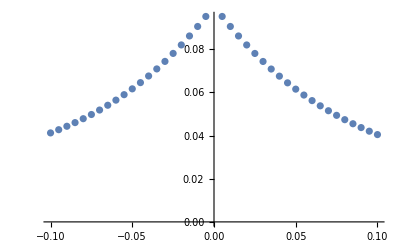

```mathematica
ListPlot[{{-0.005,0.09512195076379881},{-0.01,0.09048706321283528},{-0.015,0.08609305010884938},{-0.02,0.08193611329681039},{-0.025,0.07801105669482344},{-0.03,0.07431143879393753},{-0.035,0.07082975404481828},{-0.04,0.06755763149228766},{-0.045,0.06448603924186569},{-0.05,0.061605484576667924},{-0.055,0.05890620146719938},{-0.06,0.05637831947510352},{-0.065,0.05401201032734426},{-0.07,0.05179761048873033},{-0.075,0.04972571974983753},{-0.08,0.04778727709944797},{-0.085,0.045973616000473116},{-0.09,0.044276501653758626},{-0.095,0.04268815301757034},{-0.1,0.04120125231165617},{0.005,0.0951217971154047},{0.01,0.0904858398648195},{0.015,0.08608895367317204},{0.02,0.08192650830001502},{0.025,0.07799255330499522},{0.03,0.07427998760381105},{0.035,0.07078075178814369},{0.04,0.06748603153174326},{0.045,0.064386461199203},{0.05,0.061472318417800875},{0.055,0.058733702518785624},{0.06,0.05616069206298713},{0.065,0.05374347884648489},{0.07,0.051472477662187544},{0.075,0.04933841255652738},{0.08,0.04733238135258233},{0.085,0.045445900858668065},{0.09,0.043670935481902706},{0.095,0.04199991202546727},{0.1,0.040425723323571194}}]
```